```mathematica
ClearAll[tex,tf,mf,df,primeQpos,tr,u,id];
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
tf:=TableForm
mf:=MatrixForm
df:=Defer
primeQpos[n_]:=If[PrimeQ[n]&&n>0,True,False]
tr:=Trace
u[m_Integer]:=1
id[m_Integer]:=Floor[1/m]
```

https://math.stackexchange.com/questions/136417/what-is-so-interesting-about-the-zeroes-of-the-riemann-zeta-function/136488#136488

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes ANT

Arithmetic Functions

## Moebius Function

### Definition

The Moebius function is defined as follows:
μ(1) = 1;
if n > 1 write n as n = ∏_(i=1)^k (p^α_i)_i and
μ(n) = (-1)^k if α_i=1
μ(n) = 0 otherwise.

#### Example

```mathematica
TableForm[Table[{k,MoebiusMu[k]},{k,Divisors[60]}],TableHeadings->{None,{"k","μ[k]"}},TableAlignments->{Right}]
```

k | μ[k]
1 | 1
2 | -1
3 | -1
4 | 0
5 | -1
6 | 1
10 | 1
12 | 0
15 | 1
20 | 0
30 | -1
60 | 0

```mathematica
TableForm[Table[{k,MoebiusMu[k]},{k,1,30}],TableHeadings->{None,{"k","μ[k]"}},TableAlignments->{Right}]
```

k | μ[k]
1 | 1
2 | -1
3 | -1
4 | 0
5 | -1
6 | 1
7 | -1
8 | 0
9 | 0
10 | 1
11 | -1
12 | 0
13 | -1
14 | 1
15 | 1
16 | 0
17 | -1
18 | 0
19 | -1
20 | 0
21 | 1
22 | 1
23 | -1
24 | 0
25 | 0
26 | 1
27 | 0
28 | 0
29 | -1
30 | -1

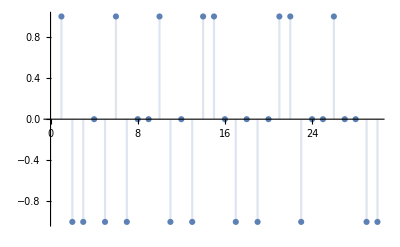

```mathematica
DiscretePlot[MoebiusMu[k],{k,30},AxesOrigin->{0,0}]
```

## Euler totient Function

### Definition

If n ≳ 1 the Euler totient ϕ(n) is defined to be the number of positive integers not exceeding n which are relatively prime to n.

Sum formula: n = ∑_(d/n) ϕ(d)

	n = ∑_(d/n) ϕ(d)
	ϕ(n) = ∑_(d/n) μ(n/d)d

Product formula: write n as n = ∏_(i=1)^k (p^α_i)_i and
	ϕ(n) = n∏_(i=1)^k (1-1/p_i)

#### Example

```mathematica
TableForm[Table[{k,EulerPhi[k]},{k,1,20}],TableHeadings->{None,{"k","ϕ[k]"}},TableAlignments->{Right}]
```

k | ϕ[k]
1 | 1
2 | 1
3 | 2
4 | 2
5 | 4
6 | 2
7 | 6
8 | 4
9 | 6
10 | 4
11 | 10
12 | 4
13 | 12
14 | 6
15 | 8
16 | 8
17 | 16
18 | 6
19 | 18
20 | 8

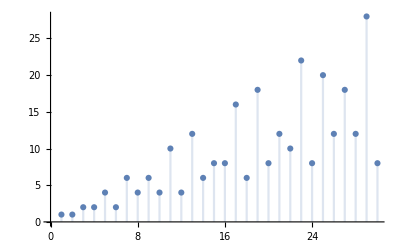

```mathematica
DiscretePlot[EulerPhi[k],{k,30},AxesOrigin->{0,0}]
```

```mathematica
Total[Map[EulerPhi[#]&,Divisors[100]]]
```

100

```mathematica
Divisors[100]
EulerPhi[100]
Total[Map[MoebiusMu[100/#]#&,Divisors[100]]]
```

{1,2,4,5,10,20,25,50,100}

40

40

## Dirichlet Multiplication ( Convolution )

### Definition

The Dirichlet convolution (f *g)(m) of two functions f(n) and g(n) is given by ∑_(d∣m) f(d) g(m/d).

#### Example

```mathematica
DirichletConvolve[MoebiusMu[n],id[n],n,12]
```

0

```mathematica
DirichletConvolve[MoebiusMu[n],u[n],n,12]
```

0

```mathematica
DirichletConvolve[MoebiusMu[n],n,n,12]
```

4

```mathematica
DirichletConvolve[MoebiusMu[n]^2 EulerPhi[n]^-1,u[n],n,12]
```

3

```mathematica
Table[{k,Log[2,DirichletConvolve[MoebiusMu[n]^2,u[n],n,k]],Total[Map[MoebiusMu[#]^2&,Divisors[k]]],2^PrimeNu[k]},{k,1,10}]//tf
```

1 | 0 | 1 | 1
2 | 1 | 2 | 2
3 | 1 | 2 | 2
4 | 1 | 2 | 2
5 | 1 | 2 | 2
6 | 2 | 4 | 4
7 | 1 | 2 | 2
8 | 1 | 2 | 2
9 | 1 | 2 | 2
10 | 2 | 4 | 4

```mathematica
DirichletConvolve[MoebiusMu[n],Log[n],n,729]//Simplify
```

Log[3]

Chebyshev

## Binomial[2n,n] is divisible by all primes n < p < 2n

#### Example

```mathematica
f[j_]:=Table[Binomial[n,k],{n,0,j},{k,0,n}]
f[20]//tf
```

1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 2 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 3 | 3 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 4 | 6 | 4 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 5 | 10 | 10 | 5 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 6 | 15 | 20 | 15 | 6 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 7 | 21 | 35 | 35 | 21 | 7 | 1 |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 8 | 28 | 56 | 70 | 56 | 28 | 8 | 1 |  |  |  |  |  |  |  |  |  |  |  | 
1 | 9 | 36 | 84 | 126 | 126 | 84 | 36 | 9 | 1 |  |  |  |  |  |  |  |  |  |  | 
1 | 10 | 45 | 120 | 210 | 252 | 210 | 120 | 45 | 10 | 1 |  |  |  |  |  |  |  |  |  | 
1 | 11 | 55 | 165 | 330 | 462 | 462 | 330 | 165 | 55 | 11 | 1 |  |  |  |  |  |  |  |  | 
1 | 12 | 66 | 220 | 495 | 792 | 924 | 792 | 495 | 220 | 66 | 12 | 1 |  |  |  |  |  |  |  | 
1 | 13 | 78 | 286 | 715 | 1287 | 1716 | 1716 | 1287 | 715 | 286 | 78 | 13 | 1 |  |  |  |  |  |  | 
1 | 14 | 91 | 364 | 1001 | 2002 | 3003 | 3432 | 3003 | 2002 | 1001 | 364 | 91 | 14 | 1 |  |  |  |  |  | 
1 | 15 | 105 | 455 | 1365 | 3003 | 5005 | 6435 | 6435 | 5005 | 3003 | 1365 | 455 | 105 | 15 | 1 |  |  |  |  | 
1 | 16 | 120 | 560 | 1820 | 4368 | 8008 | 11440 | 12870 | 11440 | 8008 | 4368 | 1820 | 560 | 120 | 16 | 1 |  |  |  | 
1 | 17 | 136 | 680 | 2380 | 6188 | 12376 | 19448 | 24310 | 24310 | 19448 | 12376 | 6188 | 2380 | 680 | 136 | 17 | 1 |  |  | 
1 | 18 | 153 | 816 | 3060 | 8568 | 18564 | 31824 | 43758 | 48620 | 43758 | 31824 | 18564 | 8568 | 3060 | 816 | 153 | 18 | 1 |  | 
1 | 19 | 171 | 969 | 3876 | 11628 | 27132 | 50388 | 75582 | 92378 | 92378 | 75582 | 50388 | 27132 | 11628 | 3876 | 969 | 171 | 19 | 1 | 
1 | 20 | 190 | 1140 | 4845 | 15504 | 38760 | 77520 | 125970 | 167960 | 184756 | 167960 | 125970 | 77520 | 38760 | 15504 | 4845 | 1140 | 190 | 20 | 1

```mathematica
Binomial[100,50]/Apply[Times,Table[Prime[k],{k,16,25}]]
```

26907494328

## Binomial[2n,n] is not divisible by any primes p > 2n

#### Example

```mathematica
Binomial[100,50]/211
```

100891344545564193334812497256/211

## Highest power of prime p in n!

```mathematica
ClearAll[f]
f[n_,p_]:=Sum[Floor[n/p^i],{i,1,Ceiling[N[Log[n]]/Log[p]]}]/;p≤n
```

```mathematica
f[10,2]
f[10,3]
f[10,5]
f[10,7]
```

8

4

2

1

```mathematica
10!
```

3628800

```mathematica
2^8 3^4 5^2 7
```

3628800

```mathematica
f[100,2]
f[100,3]
f[100,5]
f[100,7]
f[100,11]
f[100,13]
f[100,17]
f[100,19]
f[100,23]
f[100,29]
f[100,31]
f[100,37]
```

97

48

24

16

9

7

5

5

4

3

3

2

```mathematica
(100!)/(2^97 3^48 5^24 7^16 11^9 13^7 17^5 19^5 23^4 29^3 31^3 37^2 41^2 43^2 47^2 53 59 61 67 71 73 79 83 89 97)
```

1

```mathematica
f[12,2]
f[12,3]
f[12,5]
f[12,7]
f[12,11]
```

```mathematica
f[6,2]
f[6,3]
f[6,5]
```

4

2

1

```mathematica
2^2 3 7 11
```

924

```mathematica
Binomial[12,6]/(2^2 3 7 11)
```

1

```mathematica
Binomial[12,6]
```

924

```mathematica
12^PrimePi[12]
```

248832

```mathematica
(2^3 3 11 13)/Binomial[14,7]
```

1

## tmp-1

```mathematica
Simplify[Log[2^(2 n)]/Log[n],Assumptions->{n≥2}]
```

(n Log[4])/Log[n]

```mathematica
FullSimplify[2Log [2] n/Log[n],Assumptions->{n≥2}]
```

(n Log[4])/Log[n]

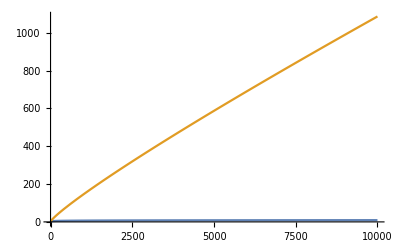

```mathematica
Plot[{Log[x],x/Log[x]},{x,2,10000},AxesOrigin->{0,0}]
```

```mathematica
10000./Log[10000]
```

1085.74

```mathematica
PrimePi[10000]
```

1229

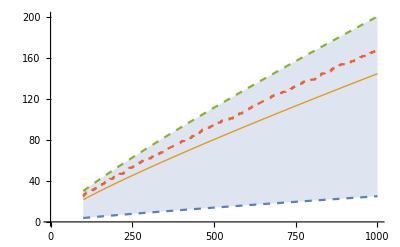

```mathematica
Plot[{1/4 Log[2.] x/Log[x],x/Log[x],2Log[2.] x/Log[x],PrimePi[x]}, {x, 100, 1000},
Filling->{1->{3}},
PlotStyle->{Dashed,Thick,Dashed},
AxesOrigin->{0,0}]
```

```mathematica
ClearAll[s,t]
s[n_]:=(Binomial[(n+1)!+n,n]-1)/((n+1)!)
t[n_]:=s[n]-(n+1)Floor[s[n]/(n+1)]
```

```mathematica
t[5]
```

137/60

```mathematica
Mod[s[6],7]
```

49/20

```mathematica
HarmonicNumber[6]
```

49/20

```mathematica
Binomial[100,50]
100^25
```

100891344545564193334812497256

100000000000000000000000000000000000000000000000000

```mathematica
1/4 Log[2.]
```

0.173287

```mathematica
6 Log[2]/Log[6.]
```

2.32112

```mathematica
14/4 Log[2]/Log[13.1]
```

0.943016

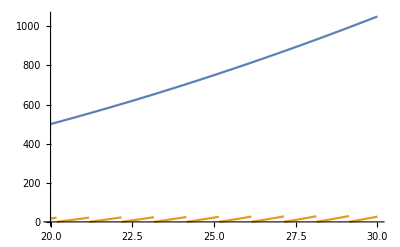

```mathematica
ClearAll[h]
h[x_]:=x^2+5x
Plot[{h[x],h[x]-(x+1)Floor[h[x]/(x+1)]},{x,20,30}]
```

```mathematica
Sum[MangoldtLambda[k]/k,{k,1,1000}]//N
```

6.32875

```mathematica
Log[1000.]
```

6.90776

```mathematica
(11^2 31 41 61-1)/(5 4 3 2)
Floor[(11^2 31 41 61-1)/(5 5 4 3 2)]
```

938125/12

15635

```mathematica
938125/12//N
```

78177.1

```mathematica
15635 5
```

78175

```mathematica
938125/12-15635 5
```

25/12

```mathematica
HarmonicNumber[4]
```

25/12

```mathematica
(Binomial[27,3]-1)/(3!)//N
```

487.333

```mathematica
(Binomial[27,3]-1)/(4!)-HarmonicNumber[3]
```

120

```mathematica
(Binomial[27,3]-1)/(4!)-4Floor[(Binomial[27,3]-1)/(4 4!)]
```

11/6

```mathematica
(Binomial[124,4]-1)/(5!)
(Binomial[124,4]-1)/(5!)-HarmonicNumber[4]
```

938125/12

78175

```mathematica
FactorInteger[78175]
```

{{5,2},{53,1},{59,1}}

```mathematica
1205656-11Floor[1205656/11]
```

1

```mathematica
Mod[1205656,11]
```

1

```mathematica
Mod[13.5,3]
```

1.5

```mathematica
13.5-3 Floor[13.5/3]
```

1.5

```mathematica
ClearAll[s,t]
s[n_]:=(Binomial[(n+1)!+n,n]-1)/((n+1)!)
t[n_]:=s[n]-(n+1)Floor[s[n]/(n+1)]
```

```mathematica
t[5]
```

137/60

```mathematica
HarmonicNumber[4]
Mod[s[2],3]
```

25/12

3/2

```mathematica
FactorInteger[Binomial[124,4]]
FactorInteger[Binomial[124,4]-1]
```

{{11,2},{31,1},{41,1},{61,1}}

{{2,1},{5,5},{19,1},{79,1}}

```mathematica
25/12 1 2 3 4
```

50

```mathematica
GeneratingFunction[1/(n+1),n,x]
```

-Log[1-x]/x

```mathematica
Series[-Log[1-x]/x,{x,0,10}]
```

1+x/2+x^2/3+x^3/4+x^4/5+x^5/6+x^6/7+x^7/8+x^8/9+x^9/10+x^10/11+O[x]^11

```mathematica
Series[-Log[1-x]/(x(1-x)),{x,0,10}]
```

1+(3 x)/2+(11 x^2)/6+(25 x^3)/12+(137 x^4)/60+(49 x^5)/20+(363 x^6)/140+(761 x^7)/280+(7129 x^8)/2520+(7381 x^9)/2520+(83711 x^10)/27720+O[x]^11

```mathematica
49 720/20
```

1764

```mathematica
5040/140
```

36

```mathematica
36 363
```

13068

```mathematica
Table[(PolyGamma[m]+EulerGamma) ,{m,1,10}]
```

{0,1,3/2,11/6,25/12,137/60,49/20,363/140,761/280,7129/2520}

```mathematica
PolyGamma[5]
```

25/12-EulerGamma

# Notes DSC

Counting

## Definitions